# Four-Pile Nim

"THE CHALLENGE"

Nim is a two-person game in which players take turns removing any number of chips from one of several piles of chips, with the goal of taking the last one. Write a function that looks at the state of a game of Nim with four piles and returns whether or not the player making the next move has a winning strategy.

## More Details

Nim is a very old game that is very easy to explain.

The setup consists of some piles of chips. As a specific example, consider four piles with 1, 2, 5, 8 chips. The game state is {1,2,5,8}.

Player 1 chooses a pile and removes some chips from that pile. In the example, Player 1 can choose pile 3 and remove from one to five chips from that pile.

Players alternate taking away chips until one player wins by taking the last chip.

Say Player 1 removes five chips from pile 3. The game state is then {1,2,0,8}. If Player 2 takes away two chips from the last pile, the game state is {1,2,0,6}. Then it is Player 1's turn, and so on.

If the game state is {0,1,0,0} for Player 1, Player 1 wins.

Because the rules of Nim are so simple and do not rely on chance, it is possible to decide if the next player to choose has a winning strategy by looking at the current game state.

For example, suppose it is Player 1's turn and the game state is {2,1}: two chips in the first pile and one chip in the second. Player 1 can win by removing one chip from pile 1, leaving the losing game state {1,1} for Player 2, who must leave Player 1 the winning game state {1,0} or {0,1}.

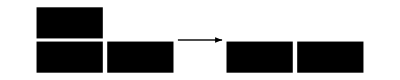

For this Challenge, you are asked to write a function that takes the starting configuration of a game of Nim with four piles and returns True or False depending on whether or not the first player to move can win, given that configuration.

## What Your Function Should Do

Write a function called NimWin that takes as input four non-negative integers (not all 0) that represent the number of chips in the starting configuration of a game of Nim with four piles. The output should be True if the first person to play from this configuration has a winning strategy and False otherwise.

This corresponds to the game state in the graphic example above:

```mathematica
NimWin[2,1,0,0]
```

True

### More Examples

```mathematica
NimWin[1,0,0,0]
```

True

```mathematica
NimWin[1, 1, 1, 1]
```

False

```mathematica
NimWin[1,3, 5, 7]
```

False

```mathematica
NimWin[1, 2, 4, 6]
```

True

```mathematica
NimWin[3, 8, 15, 2]
```

True

```mathematica
NimWin[2, 2, 5, 3]
```

True

```mathematica
NimWin[2, 2, 1, 1]
```

False

"SCRATCH AREA"

"ENTER YOUR CODE HERE"

```mathematica
NimWin[w_Integer?NonNegative,x_Integer?NonNegative,y_Integer?NonNegative,z_Integer?NonNegative]/;(x + y +z + w > 0):=If[BitXor[w,x,y,z]==0,False,True];
```